## Testing EpidemicKabu with COVID-19 data

In this notebook we count the waves for each country using the data get from EpidemicKabu .

### Getting the data

```mathematica
data=Import["/Users/linaruiz/Documents/EpidemicKabu_project/EpidemicKabu/exampleUseLibrary/data/wavesSizes.csv"];
Length@data
data[[;;10]]//Grid
data[[2;;,1]]//Union
data[[2;;,1]]//Union//Length
```

96

Country | waveNum | max | sum | spanDays | ratioSumSpan
Belgium | 0 | 0.0111486 | 0.527596 | 170 | 0.00310351
Belgium | 1 | 0.104198 | 5.15112 | 199 | 0.025885
Belgium | 2 | 0.0359951 | 3.62356 | 169 | 0.0214412
Belgium | 3 | 0.135652 | 7.52842 | 174 | 0.0432668
Belgium | 4 | 0.330276 | 14.3718 | 84 | 0.171093
Belgium | 5 | 0.0870061 | 4.53648 | 83 | 0.0546563
Belgium | 6 | 0.0539906 | 2.91928 | 98 | 0.0297885
Belgium | 7 | 0.0155236 | 0.33246 | 22 | 0.0151118
Bosnia and Herzegovina | 0 | 0.0011789 | 0.0566137 | 126 | 0.000449315

{Belgium,Bosnia and Herzegovina,Brazil,Colombia,Croatia,Ireland,Italy,Luxembourg,Norway,Republic of Korea,Romania,Spain,The United Kingdom,Türkiye,United States of America}

15

### Counting

```mathematica
totalWavesByC=MapAt[#+1&,GatherBy[data[[2;;]],First][[All,-1]][[All,{1,2}]],{All,2}]
```

{{Belgium,8},{Bosnia and Herzegovina,6},{Brazil,4},{Colombia,5},{Croatia,6},{Ireland,7},{Italy,7},{Luxembourg,9},{Norway,4},{Republic of Korea,5},{Romania,6},{Spain,8},{The United Kingdom,8},{Türkiye,6},{United States of America,6}}

Country with the highest number of waves

```mathematica
MaximalBy[totalWavesByC,Last]
```

{{Luxembourg,9}}

Country with the lowest number of waves

```mathematica
MinimalBy[totalWavesByC,Last]
```

{{Brazil,4},{Norway,4}}

Average

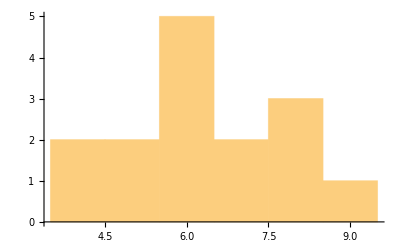
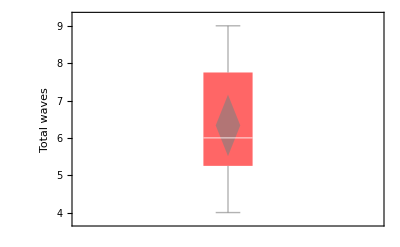
{6.33333,6.,{5.25,6.,7.75},1.49603,2.2381,-Graphics-,-Graphics-}

```mathematica
N@{Mean[#],Median[#],Quartiles[#],StandardDeviation[#],Variance[#],Histogram[#],BoxWhiskerChart[#,"Diamond",FrameLabel->{"","Total waves"},ChartStyle->Opacity[0.6,Red]]}&@totalWavesByC[[All,2]]
```